```mathematica
p1=Point[{0,0}];
p2=Point[{1,0}];
p3=Point[{.5,.5}];
```

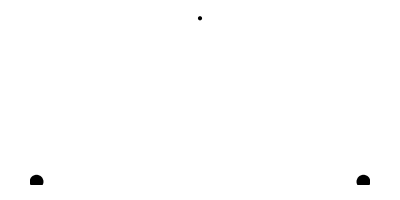

```mathematica
Show[Graphics[{{PointSize[.025],p1,p2},p3}]]
```

```mathematica
c=Circle[{1,1},Sqrt[2]];
```



```mathematica
Show[Graphics[c,Axes->Automatic,
AspectRatio->Automatic]]
```

```mathematica
r1=(10+2^(3/2))/2;
r2=(10-2^(3/2))/2;
```

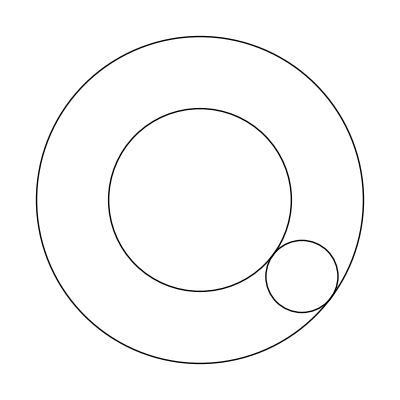

```mathematica
Show[Graphics[{c,Circle[{-3,4},r1],Circle[{-3,4},r2]},
Axes->Automatic,AspectRatio->Automatic]]
```

```mathematica
dashc1={Dashing[{.025,.025}],c1};
dashc2={Dashing[{.05,.05}],c2};
```

```mathematica
Show[Graphics[{c,dashc1,dashc2},
Axes->Automatic,AspectRatio->Automatic]]
```

-Graphics-

```mathematica
colorWheel[n_]:=
Show[Graphics[
Map[{Hue[#/(2Pi-n),Disk[{0,0},1,{#,#+n}]]}&，
Range[0,2Pi-n.n]],
AspectRatio->Automatic]]
```

```mathematica
colorWheel[Pi/256]
```

Range::range: Range specification in Range[0,2 π-π/256.π/256] does not have appropriate bounds.

-Graphics-

```mathematica
randomcoords:=Point[{Random[],Random[]}];
```

```mathematica
randomsize:=PointSize[Random[Real,{.01,.1}]]
```

```mathematica
randomcolor:=Hue[Random[]]
```

```mathematica
pts=Table[{randomcolor,randomsize,randomcoords},{330}];
```

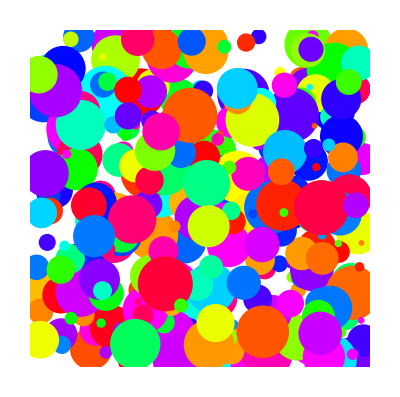

```mathematica
Show[Graphics[pts,PlotRange->All]]
```